```mathematica
Clear[ rcap, thetacap, phicap , asz, toff, axes, m, ef, hf, k, t,p, a, b, logscale] ;
rcap = {Sin[#1] Cos[#2], Sin[#1] Sin[#2], Cos[#1]} & ;
thetacap = {Cos[#1] Cos[#2], Cos[#1] Sin[#2], -Sin[#1]} &;
phicap = {-Sin[#2], Cos[#2], 0 } & ;

(*checks*)
(*{
rcap[θ, ϕ]. thetacap[θ, ϕ]// Simplify,
thetacap[θ, ϕ]. phicap[θ, ϕ],
phicap[θ, ϕ]. rcap[θ, ϕ],
rcap[θ, ϕ]× thetacap[θ, ϕ] -phicap[θ, ϕ]// Simplify } // TableForm*)

asz = 1.5 ;
toff = 0.1 ;
axes = Graphics3D[{
Red,Arrow[Tube[{{0,0,0},{asz,0,0}}] , 0.05],
Blue,Arrow[Tube[{{0,0,0},{0,asz,0}}] , 0.05],
Darker[Green, .8],Arrow[Tube[{{0,0,0},{0,0,asz}}] , 0.05],
Text[ "e_1",  {asz + toff,0,0} ],
Text[ "e_2",  {0,asz + toff,0} ],
Text[ "e_3",  {0,0,asz + toff} ]
}] ;

X[k_, t_, p_] = k Sin[t] Cos[p] ;
Y[k_, t_, p_] = k Sin[t] Sin[p] ;

m[t_, p_, k_, a_, b_] = (Cos[X[k, t,p] a/2]/(X[k, t,p]^2 - Pi^2/a^2))(2Sin[Y[k, t,p] b]/Y[k, t,p]) ;

ef[t_, p_, k_, a_, b_] = (Cos[t] Cos[p] phicap[t, p] + Sin[p]thetacap[t, p]) m[t, p, k, a, b] ;


hf[t_, p_, k_, a_, b_] = (Cos[t] Cos[p] thetacap[t, p] - Sin[p]phicap[t, p]) m[t, p, k, a, b] ;
hf[θ, ϕ, k, a, b] // Simplify // TraditionalForm

(*Assumes that x ≤1, minDb is negative (like -40 say)*)
logscale[x_, minDb_] = If[ x < 10^(minDb/ 10),minDb,10 Log10[x] ]/(-minDb) + 1 ;

(*Plot a function assumed to be in the [0,1] interval on a dB scale polar plot, with radial tick markers at -10 n dB from 0 to -40.

http://mathematica.stackexchange.com/a/79364/10

example:

PolarDbPlot[ Abs[Cos[#]] & ]
*)
PolarDbPlot := PolarPlot[ 
logscale[#1[t],-40],
{t, 0, Pi},
PolarAxesOrigin->{0,1 },
PolarGridLines->{Automatic,{1/4,2/4,3/4}},
PolarAxes->True,
PlotStyle->Thick,PolarTicks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}],{{1,0},{3/4,-10},{2/4,-20},{1/4,-30},{0,-40}}}
] & ;
```

{(2 a^2 csc^3(θ) sin(ϕ) (cos^2(θ) cot^2(ϕ)+1) sin(b k sin(θ) sin(ϕ)) cos(1/2 a k sin(θ) cos(ϕ)))/(a^2 k^3 cos^2(ϕ)-π^2 k csc^2(θ)),(2 a^2 csc(θ) cos(ϕ) sin(b k sin(θ) sin(ϕ)) cos(1/2 a k sin(θ) cos(ϕ)))/(π^2 k csc^2(θ)-a^2 k^3 cos^2(ϕ)),-(2 a^2 cos(θ) cot(ϕ) sin(b k sin(θ) sin(ϕ)) cos(1/2 a k sin(θ) cos(ϕ)))/(a^2 k^3 sin^2(θ) cos^2(ϕ)-π^2 k)}

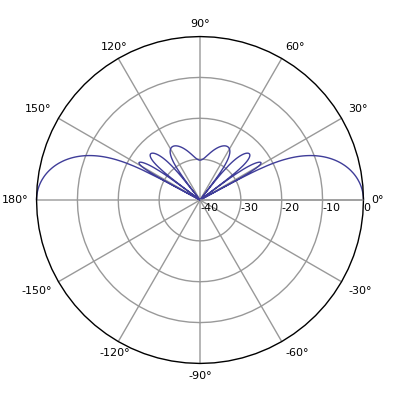
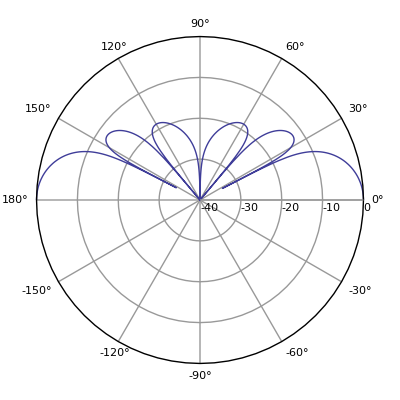
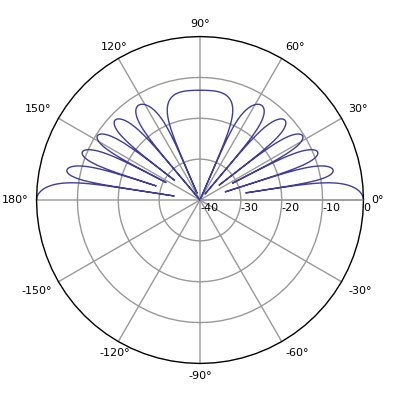
{-Graphics-,-Graphics-,-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
Module[{k,a,b, c, mv,m ,minDb},
c = 3 10^8 ;
k = 2 Pi 9.8 10^9/ c ;
a = 0.1 ;
b = 0.1 ;
mv= NMaximize[{Norm[ef[θ, ϕ, k, a, b]],0 <=θ <= Pi,0 <=ϕ ≤ 2Pi},{ θ, ϕ } ] ;
m = mv // First ;
(*ef[θ, ϕ, k, a, b] // Simplify // TraditionalForm*)
minDb = -40 ;


{(*mv,
ϕ /. (mv // Last),*)
PolarDbPlot[ 
Norm[ef[#, ϕ /. (mv // Last), k, a, b]]/m & ]
,
PolarDbPlot[ 
Norm[ef[#, 1/10^10, k, a, b]]/m & ]
,
PolarDbPlot[ Norm[ef[#, Pi/2, k, a, b]]/m & ]
(*,
PolarPlot[ Norm[ef[θ /. (mv // Last), p, k, a, b]]/m,
{p, 0, 2 Pi},
PolarAxesOrigin->{0,1 },
PolarGridLines->Automatic,PolarAxes->True,PolarTicks->{Table[{N[Pi/6 i],ToString[30 i]<>"°"},{i,-5,6}],Automatic}
]*)
,SphericalPlot3D[Norm[ef[θ, ϕ, k, a, b]]/m,{θ,0,Pi},{ϕ,0,2Pi},
PlotRange -> Full,
AxesLabel -> {x, y, z}
]
,SphericalPlot3D[
logscale[Norm[ef[θ, ϕ, k, a, b]]/m, -40],
{θ,0,Pi},
{ϕ,0,2Pi},
PlotRange -> Full,
AxesLabel -> {x, y, z}
]
(*,
 ,
SphericalPlot3D[Norm[hf[θ, ϕ, k, a, b]]/m,{θ,0,Pi},{ϕ,0,2Pi},
PlotRange -> Full,
AxesLabel -> {x, y, z}
]*)
}
]
```